# Parametric representation

This notebook requires RNL`* packages which can be downloaded from https://github.com/rnlg/RNL

```mathematica
SetDirectory[NotebookDirectory[]]
<<RNL`Vectors`
<<RNL`GMatrices`
```

/home/roman/Yandex.Disk/Students/Teaching/Спецкурс 'Петлевые интегралы'/Lectures/Lecture2

/home/roman/Programming/RNL/Source/Vectors.m

****************Vectors v1.1********************
Author:Roman N.Lee,Budker Institute of Nuclear Physics,Novosibirsk.
Vectors package defines several types:Vector,VectorIndex,TComponent.
Use Declare[{v1,v2,…},Vector] to declare variables v1,v2,… as vectors.
Use Declare[{μ,ν,…},VectorIndex] to declare variables μ,ν,… as vector indices.
See ?Vectors`* for a list of functions.

Input file hash: 272166111734557409359837133823898563385

```mathematica
SetDim[4-2ϵ](*Set dimension*)
```

```mathematica
Declare[
{l,p1,p2,q,k1,k2,k3},Vector,
{μ,ν},VectorIndex,
{m,Q,x,z,ε,s,t},Number
]
```

```mathematica
SetConstraints[{p1,p2},
sp[p1]=sp[p2]=m^2;
sp[p2-p1]=-Q^2
]
```

Executing
p1·p1=m^2;p1·p2=1/2 (2 m^2+Q^2);p2·p2=m^2;

```mathematica
SetConstraints[{k1,k2,k3},
sp[k1]=sp[k2]=sp[k3]=sp[k1+k2-k3]=0;
sp[k1+k2]=s;sp[k1-k3]=t; (*T is positive*)
]
```

Executing
k1·k1=0;k1·k2=s/2;k1·k3=-t/2;k2·k2=0;k2·k3=(s+t)/2;k3·k3=0;

Convenience abbreviation:

```mathematica
SimplifyGTrace=Factor@*LFDistribute@*DummyEliminate@*GTrace;
```

A smarter version of Mathematica’s PowerExpand function:

```mathematica
PowExpand::usage="PowExpand[expr,cond] expands powers  in expr assuming cond holds.";
PowExpand[expr_,cond_:True]:=expr/.Power[ex_,e_]:>Module[{fl},fl=Replace[Replace[FactorList[ex],{n_Integer,k_Integer}:>Sequence@@({#1,k*#2}&@@@FactorInteger[n]),{1}],
{{n_,k_Integer}/;TrueQ[Quiet@Simplify[n>0,cond]]:>{n,k},{n_,k_Integer}/;TrueQ[Quiet@Simplify[n<0,cond]]:>{-n,k},_:>Sequence[]},{1}];Times@@(#^(#2*e)&@@@fl)*Factor[ex/(Times@@Power@@@fl)]^e]
```

## Some generic 1-loop examples

### 1-loop massive tadpole master

```mathematica
{repr,xs}=ParametricRepresentation[1,{{m^2-sp[l],α}},{l},Sign->Minus]
```

{(x1^(-5+2 α+2 ϵ) (m^2 x1^2)^(2-α-ϵ) Gamma[-2+α+ϵ])/Gamma[α],{x1}}

```mathematica
repr/.x1->1
```

((m^2)^(2-α-ϵ) Gamma[-2+α+ϵ])/Gamma[α]

### 1-loop massless sunrise master

```mathematica
{repr,xs}=ParametricRepresentation[1,{{-sp[l],α},{-sp[q-l],2}},{l},Sign->Minus]
```

{(x1^(-1+α) x2 (x1+x2)^(-2+α+2 ϵ) Gamma[α+ϵ] (-x1 x2 q·q)^(-α-ϵ))/Gamma[α],{x1,x2}}

```mathematica
Integrate[repr/.x2->1-x1,{x1,0,1},GenerateConditions->False]
```

-(π (-1+α+ϵ) Csc[π (α+ϵ)] Gamma[-ϵ] (-(q·q))^(-α-ϵ))/(Gamma[α] Gamma[2-α-2 ϵ])

### 1-loop onshell self-energy master

```mathematica
{repr,xs}=ParametricRepresentation[1,{{-sp[l],α},{m^2-sp[p1-l],β}},{l},Sign->Minus]
```

{(x1^(-1+α) x2^(-1+β) (m^2 x2^2)^(2-α-β-ϵ) (x1+x2)^(-4+α+β+2 ϵ) Gamma[-2+α+β+ϵ])/(Gamma[α] Gamma[β]),{x1,x2}}

```mathematica
Integrate[repr/.x2->1-x1,{x1,0,1},GenerateConditions->False]
```

((m^2)^(2-α-β-ϵ) Gamma[4-2 α-β-2 ϵ] Gamma[-2+α+β+ϵ])/(Gamma[β] Gamma[4-α-β-2 ϵ])

### 1-loop HQET self-energy master

```mathematica
{repr,xs}=PowerExpand[ParametricRepresentation[1,{{-sp[l],α},{2sp[p1/m,l]+ε,1}},{l},Sign->Minus]]
```

{(x1^(-4+2 α+2 ϵ) (x2^2+x1 x2 ε)^(1-α-ϵ) Gamma[-1+α+ϵ])/Gamma[α],{x1,x2}}

```mathematica
Integrate[repr/.x2->1-x1,{x1,0,1},GenerateConditions->False]
```

(ε^(3-2 α-2 ϵ) Gamma[2-α-ϵ] Gamma[-3+2 α+2 ϵ])/Gamma[α]

### 1-loop massless vertex with two on-shell legs master

```mathematica
Block[{m=0},
{repr,xs}=ParametricRepresentation[1,{{-sp[l],α},{-sp[p2-l],β},{-sp[p1-l],γ}},{l},Sign->Minus]]
```

{(x1^(-1+α) x2^(-1+β) x3^(-1+γ) (Q^2 x2 x3)^(2-α-β-γ-ϵ) (x1+x2+x3)^(-4+α+β+γ+2 ϵ) Gamma[-2+α+β+γ+ϵ])/(Gamma[α] Gamma[β] Gamma[γ]),{x1,x2,x3}}

```mathematica
Integrate[Integrate[repr/.x3->1-x2,{x1,0,∞},GenerateConditions->False],{x2,0,1},GenerateConditions->False]
```

(Q^4 (Q^2)^(-α-β-γ-ϵ) Gamma[2-α-β-ϵ] Gamma[2-α-γ-ϵ] Gamma[-2+α+β+γ+ϵ])/(Gamma[β] Gamma[γ] Gamma[4-α-β-γ-2 ϵ])

### 1-loop box

```mathematica
Block[{m=0},
{repr,xs}=ParametricRepresentation[1,{{-sp[l],1+α},{-sp[l-k1],1+β},{-sp[k2+l],1+γ},{-sp[l-k1+k3],1+δ}},{l},Sign->Minus]]
```

{(x1^α x2^β x3^γ x4^δ (x1+x2+x3+x4)^(α+β+γ+δ+2 ϵ) (-s x2 x3-t x1 x4)^(-2-α-β-γ-δ-ϵ) Gamma[2+α+β+γ+δ+ϵ])/(Gamma[1+α] Gamma[1+β] Gamma[1+γ] Gamma[1+δ]),{x1,x2,x3,x4}}

```mathematica
ex1=Simplify[repr*y/.{x2->1-x3,x1->y x1,x4->y(1-x1)}]
```

((1-x3)^β x3^γ y (x1 y)^α (1+y)^(α+β+γ+δ+2 ϵ) (y-x1 y)^δ (s (-1+x3) x3+t (-1+x1) x1 y^2)^(-2-α-β-γ-δ-ϵ) Gamma[2+α+β+γ+δ+ϵ])/(Gamma[1+α] Gamma[1+β] Gamma[1+γ] Gamma[1+δ])

We’ll need Mellin-Barnes parametrization (Γ(ν))/(A+B)^ν=∫_(ν_0-i∞)^(ν_0+i∞) dz/(2πi)(Γ(z))/A^z(Γ(ν-z))/B^(ν-z), (0<c<ν).

```mathematica
ex2=Simplify@ PowExpand[ex1*(Gamma[z]/(s (-1+x3) x3)^z Gamma[ν-z]/((t (-1+x1) x1 y^2)^(ν-z))/(Γ[ν]/((s (-1+x3) x3+t (-1+x1) x1 y^2)^ν))/.ν->2+α+β+γ+δ+ϵ),y>0&&0<x1<1&&0<x3<1]
```

((-s)^-z (-t)^(-2+z-α-β-γ-δ-ϵ) (1-x1)^(-2+z-α-β-γ-ϵ) x1^(-2+z-β-γ-δ-ϵ) (1-x3)^(-z+β) x3^(-z+γ) y^(-3+2 z-α-2 β-2 γ-δ-2 ϵ) (1+y)^(α+β+γ+δ+2 ϵ) Gamma[z] Gamma[2+α+β+γ+δ+ϵ] Gamma[2-z+α+β+γ+δ+ϵ])/(Gamma[1+α] Gamma[1+β] Gamma[1+γ] Gamma[1+δ] Γ[2+α+β+γ+δ+ϵ])

```mathematica
ex3=Integrate[Echo@Integrate[Echo@Integrate[ex2,{x3,0,1},GenerateConditions->False],{x1,0,1},GenerateConditions->False],{y,0,∞},GenerateConditions->False]
```

((-s)^-z (-t)^(-2+z-α-β-γ-δ-ϵ) (1-x1)^(-2+z-α-β-γ-ϵ) x1^(-2+z-β-γ-δ-ϵ) y^(-3+2 z-α-2 β-2 γ-δ-2 ϵ) (1+y)^(α+β+γ+δ+2 ϵ) Gamma[z] Gamma[1-z+β] Gamma[1-z+γ] Gamma[2+α+β+γ+δ+ϵ] Gamma[2-z+α+β+γ+δ+ϵ])/(Gamma[1+α] Gamma[1+β] Gamma[1+γ] Gamma[2-2 z+β+γ] Gamma[1+δ] Γ[2+α+β+γ+δ+ϵ])

((-s)^-z (-t)^(-2+z-α-β-γ-δ-ϵ) y^(-3+2 z-α-2 β-2 γ-δ-2 ϵ) (1+y)^(α+β+γ+δ+2 ϵ) Gamma[z] Gamma[1-z+β] Gamma[1-z+γ] Gamma[-1+z-α-β-γ-ϵ] Gamma[-1+z-β-γ-δ-ϵ] Gamma[2+α+β+γ+δ+ϵ] Gamma[2-z+α+β+γ+δ+ϵ])/(Gamma[1+α] Gamma[1+β] Gamma[1+γ] Gamma[2-2 z+β+γ] Gamma[1+δ] Gamma[-2+2 z-α-2 β-2 γ-δ-2 ϵ] Γ[2+α+β+γ+δ+ϵ])

((-s)^-z (-t)^(-2+z-α-β-γ-δ-ϵ) Gamma[z] Gamma[1-z+β] Gamma[1-z+γ] Gamma[-1+z-α-β-γ-ϵ] Gamma[-1+z-β-γ-δ-ϵ] Gamma[2+α+β+γ+δ+ϵ] Gamma[2-z+α+β+γ+δ+ϵ])/(Gamma[1+α] Gamma[1+β] Gamma[1+γ] Gamma[1+δ] Gamma[-α-β-γ-δ-2 ϵ] Γ[2+α+β+γ+δ+ϵ])

Now we can close the vertical contour to the right and write the integral as sum over residues. 
For simplicity we assume that α,β,γ,δ,ϵ are all small, so ν=2 + α + β + γ + δ + ϵ is close to 2. Thus we can take ν_0=1 and account for poles to the right from 1. 
Examining the arguments of Γ-functions, we see the series of poles at z=1+β+n,1+γ+n,2+α+β+γ+δ+ϵ-n. Fortunately, they are all simple poles, so we can easily evaluate the residue for generic n. Below we do this by simply replacing Γ(-n)->(-1)^n/n! (this is minus the residue of Γ(-z) at z=n, but the sign is cancelled by the negative direction of the contour).

```mathematica
result=Sum[ex3/.z->1+β+n/.Gamma[-n]->(-1)^n/n!,{n,0,∞}]
+Sum[ex3/.z->1+γ+n/.Gamma[-n]->(-1)^n/n!,{n,0,∞}]
+Sum[ex3/.z->2+α+β+γ+δ+ϵ+n/.Gamma[-n]->(-1)^n/n!,{n,0,∞}]
```

((-s)^-β (-t)^(-α-γ-δ-ϵ) Gamma[-β+γ] Gamma[-α-γ-ϵ] Gamma[-γ-δ-ϵ] Gamma[1+α+γ+δ+ϵ] Gamma[2+α+β+γ+δ+ϵ] HypergeometricPFQ[{1+β,-α-γ-ϵ,-γ-δ-ϵ},{1+β-γ,-α-γ-δ-ϵ},-t/s])/(s t Gamma[1+α] Gamma[1+γ] Gamma[1+δ] Gamma[-α-β-γ-δ-2 ϵ] Γ[2+α+β+γ+δ+ϵ])

((-s)^-γ (-t)^(-α-β-δ-ϵ) Gamma[β-γ] Gamma[-α-β-ϵ] Gamma[-β-δ-ϵ] Gamma[1+α+β+δ+ϵ] Gamma[2+α+β+γ+δ+ϵ] HypergeometricPFQ[{1+γ,-α-β-ϵ,-β-δ-ϵ},{1-β+γ,-α-β-δ-ϵ},-t/s])/(s t Gamma[1+α] Gamma[1+β] Gamma[1+δ] Gamma[-α-β-γ-δ-2 ϵ] Γ[2+α+β+γ+δ+ϵ])

((-s)^(-α-β-γ-δ-ϵ) Gamma[-1-α-β-δ-ϵ] Gamma[-1-α-γ-δ-ϵ] Gamma[2+α+β+γ+δ+ϵ]^2 HypergeometricPFQ[{1+α,1+δ,2+α+β+γ+δ+ϵ},{2+α+β+δ+ϵ,2+α+γ+δ+ϵ},-t/s])/(s^2 Gamma[1+β] Gamma[1+γ] Gamma[-α-β-γ-δ-2 ϵ] Γ[2+α+β+γ+δ+ϵ])

## 1-loop electron form factors

### Finding projectors

Let us first find the projectors for F1 and F2 factors. We remind that the matrix element of the current has the form j_μ=ū(p_2)[γ_μ F_1(q^2)-(γ_μ q̂-q̂ γ_μ)/(4m)F_2(q^2)]u(p_1).
We should take into account that the spinors satisfy Dirac equation, thus we search for projectors  P_(1,2)^μ which satisfy 1/4 Tr{[γ_μ F_1-(γ_μ q̂-q̂ γ_μ)/(4m)F_2]((p̂)_1+m)P_(1,2)^μ((p̂)_1+m)}=F_(1,2)

```mathematica
Declare[{a,b},Number];
Pr=(a γ^μ+b ((γ^μ).q̂-q̂.γ^μ));
```

```mathematica
Block[{q=p2-p1},
{eq1=SimplifyGTrace[Subscript[γ, μ].(OverHat[p1]+m Subscript[I, γ]).Pr.(OverHat[p2]+m Subscript[I, γ])],eq2=SimplifyGTrace[-1/(4m)(Subscript[γ, μ].q̂-q̂.Subscript[γ, μ]).(OverHat[p1]+m Subscript[I, γ]).Pr.(OverHat[p2]+m Subscript[I, γ])]}
]
```

{2 a m^2-a Q^2-6 b m Q^2+a Q^2 ϵ+4 b m Q^2 ϵ,(Q^2 (-3 a m-8 b m^2+b Q^2+2 a m ϵ+8 b m^2 ϵ))/(2 m)}

```mathematica
Pr1=FullSimplify@LFDistribute[Pr/.Solve[{eq1==1,eq2==0},{a,b}][[1]]]
```

(m (-3+2 ϵ) (q̂.γ^μ-γ^μ.q̂)+(Q^2+8 m^2 (-1+ϵ)) γ^μ)/((4 m^2+Q^2)^2 (-1+ϵ))

```mathematica
Pr2=FullSimplify@LFDistribute[Pr/.Solve[{eq1==0,eq2==1},{a,b}][[1]]]
```

(-2 m (2 m^2+Q^2 (-1+ϵ)) (q̂.γ^μ-γ^μ.q̂)+4 m^2 Q^2 (3-2 ϵ) γ^μ)/((4 m^2 Q+Q^3)^2 (-1+ϵ))

Check that the projectors work as expected:

```mathematica
Declare[{F1,F2},Number];
Block[{q=p2-p1},
{SimplifyGTrace[(Subscript[γ, μ] F1-1/(4m)(Subscript[γ, μ].q̂-q̂.Subscript[γ, μ])F2).(OverHat[p1]+m Subscript[I, γ]).Pr1.(OverHat[p2]+m Subscript[I, γ])],SimplifyGTrace[(Subscript[γ, μ] F1-1/(4m)(Subscript[γ, μ].q̂-q̂.Subscript[γ, μ])F2).(OverHat[p1]+m Subscript[I, γ]).Pr2.(OverHat[p2]+m Subscript[I, γ])]}]
```

{F1,F2}

### One-loop form factors

```mathematica
num=(γ^ν).(OverHat[p2]-l̂+m Subscript[I, γ]).Subscript[γ, μ].(OverHat[p1]-l̂+m Subscript[I, γ]).Subscript[γ, ν];
den=(sp[p2-l]-m^2+i0)(sp[p1-l]-m^2+i0)(sp[l]+i0);
```

#### F2

Using Mathematica only (slow)

Using FORM (fast)
NB: this code requires “form” command available from the terminal.

```mathematica
Block[{q=p2-p1},
If[Quiet[RunProcess["form"]]=!=$Failed,
ex1=Simplify[FORMTraces[gTrace[num.(OverHat[p1]+m Subscript[I, γ]).Numerator[Pr2].(OverHat[p2]+m Subscript[I, γ])]]/(den Denominator[Pr2])],
ex1=Simplify[1/den SimplifyGTrace[num.(OverHat[p1]+m Subscript[I, γ]).Pr2.(OverHat[p2]+m Subscript[I, γ])]]
]]
```

-(8 m^2 ((4 m^2 Q^2+Q^4) l·l+2 (2 m^2+Q^2 (-1+ϵ)) (l·p1)^2+l·p1 (4 m^2 Q^2+Q^4+(-8 m^2+4 Q^2 (-2+ϵ)) l·p2)+l·p2 (4 m^2 Q^2+Q^4+2 (2 m^2+Q^2 (-1+ϵ)) l·p2)))/((4 m^2 Q+Q^3)^2 (i0+l·l) (i0-m^2+(-l+p1)·(-l+p1)) (i0-m^2+(-l+p2)·(-l+p2)))

```mathematica
{repr,xs}=ParametricRepresentation[ex2,{l},Contours->i0,Sign->Minus]
```

{4 (x1+x2+x3)^(-3+2 ϵ) (m^2 x2^2+2 m^2 x2 x3+Q^2 x2 x3+m^2 x3^2)^(-1-ϵ) (m^2 x1 x2+m^2 x1 x3+m^2 x2^2 ϵ+2 m^2 x2 x3 ϵ+m^2 x3^2 ϵ) Gamma[1+ϵ],{x1,x2,x3}}

```mathematica
repr0=FullSimplify[repr/.ϵ->0]
```

(4 m^2 x1 (x2+x3))/((x1+x2+x3)^3 (Q^2 x2 x3+m^2 (x2+x3)^2))

```mathematica
F2result=α/(4π)Simplify[Integrate[Integrate[repr0/.{x3->1-x2},{x1,0,∞},GenerateConditions->False],{x2,0,1},GenerateConditions->False],Assumptions->Q>0&&m>0]
```

(2 m^2 α ArcTanh[Q/(√(4 m^2+Q^2))])/(π Q √(4 m^2+Q^2))

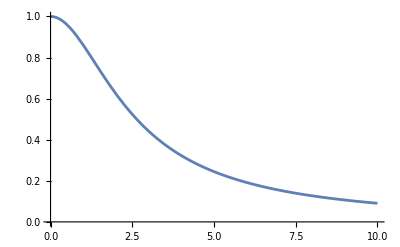

```mathematica
Plot[F2result/(α/(2π))/.m->1,{Q,0,10}]
```

```mathematica
Series[F2result,{Q,0,0}]
```

α/(2 π)+O[Q]^1

```mathematica
NotebookSave[]
```

#### F1

Using FORM (fast)

```mathematica
Block[{q=p2-p1},
If[Quiet[RunProcess["form"]]=!=$Failed,
ex1=Simplify[FORMTraces[gTrace[num.(OverHat[p1]+m Subscript[I, γ]).Numerator[Pr1].(OverHat[p2]+m Subscript[I, γ])]]/(den Denominator[Pr1])],
ex1=Simplify[1/den SimplifyGTrace[num.(OverHat[p1]+m Subscript[I, γ]).Pr1.(OverHat[p2]+m Subscript[I, γ])]]
]]
```

(2 (32 m^6+32 m^4 Q^2+10 m^2 Q^4+Q^6-(4 m^2+Q^2) (4 m^2 (-1+ϵ)+Q^2 ϵ) l·l+4 m^2 (-3+2 ϵ) (l·p1)^2-16 m^4 l·p2-12 m^2 Q^2 l·p2-2 Q^4 l·p2-12 m^2 (l·p2)^2+8 m^2 ϵ (l·p2)^2-2 l·p1 (8 m^4+6 m^2 Q^2+Q^4-2 (Q^2+m^2 (-2+4 ϵ)) l·p2)))/((4 m^2+Q^2)^2 (i0+l·l) (i0-m^2+(-l+p1)·(-l+p1)) (i0-m^2+(-l+p2)·(-l+p2)))

```mathematica
{repr,xs}=ParametricRepresentation[ex1,{l},Contours->i0,Sign->Minus,Method->"UF"]
```

{-(2 (x1+x2+x3)^(-3+2 ϵ) (m^2 x2^2+2 m^2 x2 x3+Q^2 x2 x3+m^2 x3^2)^(-1-ϵ) (-m^2 x2^2-2 m^2 x2 x3-Q^2 x2 x3-m^2 x3^2+2 m^2 x1^2 ϵ+Q^2 x1^2 ϵ+2 m^2 x1 x2 ϵ+Q^2 x1 x2 ϵ+m^2 x2^2 ϵ+2 m^2 x1 x3 ϵ+Q^2 x1 x3 ϵ+2 m^2 x2 x3 ϵ+3 Q^2 x2 x3 ϵ+m^2 x3^2 ϵ-2 Q^2 x2 x3 ϵ^2) Gamma[1+ϵ])/ϵ,{x1,x2,x3}}

```mathematica
F1result=FunctionExpand@Integrate[Integrate[repr/.x3->1-x2,{x1,0,∞},GenerateConditions->False],{x2,0,1},GenerateConditions->False]//TraditionalForm
```

-1/(2 Q^2 (ϵ-1) ϵ^2 (4 ϵ-2) √(4 m^2 Q^2+Q^4))(m^2)^(-ϵ-1) ϵ+1 ((√(4 m^2 Q^2+Q^4)+Q^2) (1/2-Q^2/(2 √(4 m^2 Q^2+Q^4)))^ϵ (-(ϵ-1) (√(4 m^2 Q^2+Q^4)-Q^2) (m^2 (-4 ϵ^2+2 ϵ+2)+Q^2) -ϵϵ+11-ϵQ^2/(2 √(Q^4+4 m^2 Q^2))+1/2-2 ϵ √(4 m^2 Q^2+Q^4) (m-2 m ϵ)^2 1-ϵϵ2-ϵQ^2/(2 √(Q^4+4 m^2 Q^2))+1/2)-2^-ϵ (√(4 m^2 Q^2+Q^4)-Q^2) (Q^2/(√(4 m^2 Q^2+Q^4))+1)^ϵ (-(ϵ-1) (√(4 m^2 Q^2+Q^4)+Q^2) (m^2 (-4 ϵ^2+2 ϵ+2)+Q^2) -ϵϵ+11-ϵ1/2-Q^2/(2 √(Q^4+4 m^2 Q^2))-2 ϵ √(4 m^2 Q^2+Q^4) (m-2 m ϵ)^2 1-ϵϵ2-ϵ1/2-Q^2/(2 √(Q^4+4 m^2 Q^2))))

```mathematica
NotebookSave[]
```